FittedModel[2423.23+147.368 x-11.4125 x^2]

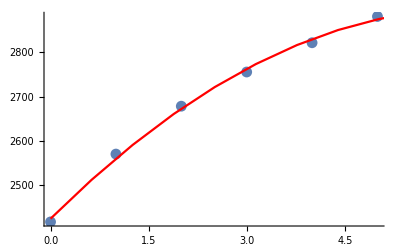

0.999992

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
name := "where-nq"
data :=Import[StringJoin["/Users/greg/Documents/School/Science_Research/workspace/ODRA-with-Enums/greg/queries/benchmarks-",name,".csv"], "Table", {"FieldSeparators" -> ";"}][[All,{1,3}]]
nlm = NonlinearModelFit[data, a+b*x+c*x^2,{a,b,c},x]
Show[ListPlot[data],Plot[nlm[x],{x,0,2048},PlotStyle->Red]]
nlm["RSquared"]
```